# Teubner.f conversion factor

```mathematica
α = 1/137;
teubnerFactor = -3/α
teubner2Gev = -0.005554;
teubner2Gev teubnerFactor
```

-411

2.28269

# Experimental Integral

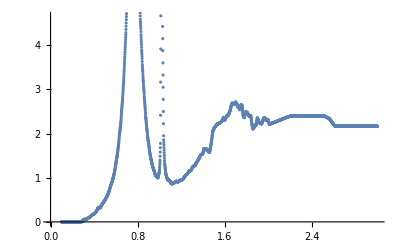

InterpolatingFunction::dmvali: The integration endpoint TraditionalForm`0 in dimension TraditionalForm`1 lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmvali: The integration endpoint TraditionalForm`3 in dimension TraditionalForm`1 lies outside the range of data in the interpolating function. Extrapolation will be used.

6.12525

```mathematica
data = Import["/Users/Knowledge/Developer/ROOT/Experiment/data.dat", "Table"];
ListPlot[data]
Integrate[Interpolation[data,InterpolationOrder->2][x],{x,0,3}]
```

# Running of the strong coupling α_s

```mathematica
b0=(33-2*nf)/12/Pi;
b1= (153-19*nf)/24/Pi^2;
b2=(2857-5033/9*nf+325/27*nf^2)/128/Pi^3;
```

```mathematica
DSolve[-x*y'[x]==b0*y[x]^2+b1*y[x]^3+b2*y[x]^4, y[x], x]
```

{{y(x)→InverseFunction[((2 (b1^2-2 b0 b2) tan^-1((2 #1 b2+b1)/(√(4 b0 b2-b1^2))))/(√(4 b0 b2-b1^2))+b1 log(#1 (#1 b2+b1)+b0)-(2 b0)/#1-2 b1 log(#1))/(2 b0^2)&][c_1-log(x)]}}

```mathematica
DSolve[-x*y'[x]==b0*y[x]^2,y[x], x]
```

{{y(x)→1/(b0 log(x)-c_1)}}